{{x→(m1 x1-y1)/m1}}

{{x→(m2 x3-y3)/m2}}

-m1 x1+y1==-m2 x3+y3

--

m2 (x1-x3)+y3

m1 (-x1+x3)+y1

--

(m1 x1-m2 x3-y1+y3)/(m1-m2)

(-m2 y1+m1 (m2 (x1-x3)+y3))/(m1-m2)

(y1-y2)/(x1-x2)==(y3-y4)/(x3-x4)

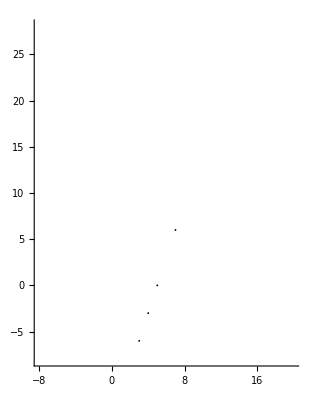

```mathematica
ClearAll["Global`*"];
nRad=.1;
p1={x1,y1};
p2={x2,y2};
p3={x3,y3};
p4={x4,y4};


y1[x_]:=m1(x-x1)+y1;
y2[x_]:=m2(x-x3)+y3;
Solve[y1[x]==0,x]
Solve[y2[x]==0,x]
y1[0]==y2[0]

Print["--"]
y2[x1]
y1[x3]
Print["--"]
S=Solve[y1[x]==y2[x],x];
Px=S[[1]][[1]][[2]]//Simplify
Py=y1[Px]//Simplify

m1=(y1-y2)/(x1-x2);
m2=(y3-y4)/(x3-x4);
m1==m2
{x1,y1,x2,y2,x3,y3,x4,y4}={2, 0, 2, 27, 1, 5, 18, 5};
{x1,y1,x2,y2,x3,y3,x4,y4}={5, 0, 7, 6, 3,-6, 4,-3};


d1=Graphics[{Black,Disk[p1,nRad]}];
d2=Graphics[{Black,Disk[p2,nRad]}];
d3=Graphics[{Black,Disk[p3,nRad]}];
d4=Graphics[{Black,Disk[p4,nRad]}];
Show[
d1,d2,d3,d4,
Axes->True,
AspectRatio->Automatic,
PlotRange->{{-8,20},{-8,28}}
]
```